```mathematica
Matrix1 = {{1,-3, 3},{3,-5,3},{6,-6,4}}; (*input matrix*)
Matrix1 //MatrixForm (*printing the input matrix in standard form*)
```

(1 | -3 | 3
3 | -5 | 3
6 | -6 | 4)

```mathematica
Matrix2 = Transpose[Matrix1];(*Taking the transpose of a matrix*)
Matrix2 //MatrixForm
```

(1 | 3 | 6
-3 | -5 | -6
3 | 3 | 4)

```mathematica
Matrix3 = Inverse[Matrix1];(*Taking the inverse of a matrix*)
Matrix3 //MatrixForm
```

(-1/8 | -3/8 | 3/8
3/8 | -7/8 | 3/8
3/4 | -3/4 | 1/4)

```mathematica
DeterminantValue = Det[Matrix1](*Finding the determinant*)
```

16

```mathematica
Eigen = Eigensystem[Matrix1];(*Finding the eigensystem of the matrix*)
Eigen // MatrixForm
```

(4 | -2 | -2
{1,1,2} | {-1,0,1} | {1,1,0})

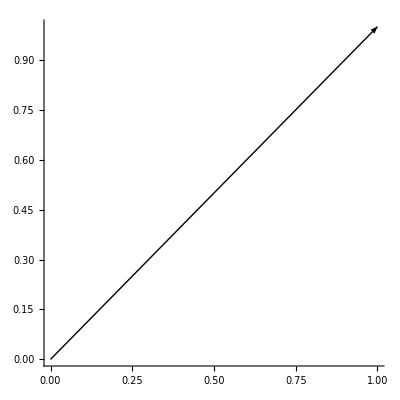

```mathematica
(*Rotation of a 2D vector*)
vector1 = {1,1};
Graphics[{Arrow[{{0,0},vector1}]},Axes->True](*Plot the vector in 2 Dimensional space*)
```

```mathematica
(*Now let's we want to rotate vector1 by some user inputted angle in the counterclockwise direction*)
(*We use matrices!*)
```

```mathematica
angle = Input["Enter angle in radians"];(*User inputted rotation angle*)
RotationMat = RotationMatrix[angle];(*We find the rotation matrix*)
RotationMat//MatrixForm
```

((√3)/2 | -1/2
1/2 | (√3)/2)

```mathematica
NewVector = RotationMat.vector1;
NewVector //MatrixForm
```

(-1/2+(√3)/2
1/2+(√3)/2)

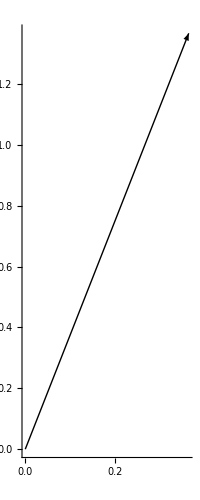

```mathematica
Graphics[{Arrow[{{0,0},NewVector}]},Axes->True](*Plot the vector in 2 Dimensional space*)
```

```mathematica
(*Now we go to the 3-Dimensional case*)
```

```mathematica
vec1 = {1,2,3};
vec2 = {4,5,6};
vec3 = {5,6,7};
```

```mathematica
Graphics3D[Arrow[{{0,0,0},vec1}],Axes->True,AxesLabel->{"X","Y","Z"},ImageSize->Medium]
```

-Graphics3D-

```mathematica
Graphics3D[Arrow[{{0,0,0},vec2}],Axes->True,AxesLabel->{"X","Y","Z"},ImageSize->Medium]
```

-Graphics3D-

```mathematica
Graphics3D[Arrow[{{0,0,0},vec3}],Axes->True,AxesLabel->{"X","Y","Z"},ImageSize->Medium]
```

-Graphics3D-

```mathematica
data={vec1,vec2,vec3};

Graphics3D[Arrow[{{0,0,0},#}]&/@data,Axes -> True,AxesLabel->{x,y,z}]
```

-Graphics3D-

```mathematica
(*We can plot them together*)
```

```mathematica
(*Now say we want to rotate vec1 around the z axis by some user inputted angle*)
angleZ = Input["Enter angle in radians"];
Rotationz = RotationMatrix[angleZ, {0,0,1}];
Rotationz//MatrixForm
```

(-1 | 0 | 0
0 | -1 | 0
0 | 0 | 1)

```mathematica
RotatedVec1 = Rotationz.vec1;
RotatedVec1//MatrixForm
```

(-1
-2
3)

```mathematica
Graphics3D[Arrow[{{0,0,0},RotatedVec1}],Axes->True,AxesLabel->{"X","Y","Z"},ImageSize->Large]
```

-Graphics3D-

```mathematica
(*In real game development, however, rotations are not that easy. You usually don't rotate about a fixed axes but need one vector to rotate in the direction of another vector*)
vec = Input["Enter the direction you want to rotate vec2 in"];
rotatemat2 = RotationMatrix[{vec2,vec}];
rotatemat2//MatrixForm;
```

```mathematica
(*Let's plot the rotated vec2*)
```

```mathematica
RotatedVec2 = rotatemat2.vec2;
RotatedVec2//MatrixForm
```

(4
5
6)

```mathematica
Graphics3D[Arrow[{{0,0,0},RotatedVec2}],Axes->True,AxesLabel->{"X","Y","Z"},ImageSize->Large](*Plotting the new matrix*)
```

-Graphics3D-

```mathematica
rotate1 = RotationMatrix[{vec1,vec2}];(*gives the matrix that rotates vec1 in the direction of vec2*)
rotate1 //MatrixForm
```

(1/462 (77+80 √22) | 1/462 (-154+41 √22) | 1/462 (77+2 √22)
1/462 (-154+23 √22) | 2/231 (77+8 √22) | 1/462 (-154+41 √22)
1/462 (77-34 √22) | 1/462 (-154+23 √22) | 1/462 (77+80 √22))

```mathematica
Graphics3D[{Opacity[1],Cuboid[{-.5,-.5,-.5}]},Boxed->False](*Plotting just a plain cuboid*)
```

-Graphics3D-

```mathematica
Graphics3D[{{Opacity[1],Cuboid[{-.5,-.5,-.5}]},GeometricTransformation[Cuboid[{-.5,-.5,-.5}],rotate1]},Boxed->False](*Now plotting the same cuboid that is rotated by the vector rotate1*)
```

-Graphics3D-

```mathematica
rotate2 = RotationMatrix[{vec2,vec3}];(*gives the matrix that rotates vec2 in the direction of vec3*)
rotate2//MatrixForm
```

(1/462 (77+46 √70) | 1/462 (-154+19 √70) | 1/462 (77-8 √70)
(-770+89 √70)/2310 | (2 (385+23 √70))/1155 | 1/462 (-154+19 √70)
(385-52 √70)/2310 | (-770+89 √70)/2310 | 1/462 (77+46 √70))

```mathematica
Graphics3D[{{Opacity[1],Cuboid[{-.5,-.5,-.5}]},GeometricTransformation[Cuboid[{-.5,-.5,-.5}],rotate2]},Boxed->False](*Now plotting the same cuboid that is rotated by the vector rotate1*)
```

-Graphics3D-

```mathematica
Manipulate[ Graphics[{{Thick,Line[Choose]}, {Thick,RGBColor[0,.5,.6],Line[{{x1,y1},{x2,y2}}.#&/@Choose]}},Axes->True,PlotRange->{{-10,10},{-10,10}},m=Invisible[MatrixForm[{{1/2,0},{1/2,0}}]]; PlotLabel->Style[Row[{m MatrixForm[{{Style["a",Italic],Style["b",Italic]},{Style["c",Italic],Style["d",Italic]}}]}]==Row[{MatrixForm[{{x1,y1},{x2,y2}}],m}],20],ImageSize->{500,350}], Row[{"How does changing ",Text@Style["a",Italic],", ",Text@ Style["b",Italic], ", ",Text@Style["c",Italic],", or ", Text@Style["d",Italic], " change the figure?"}], {{x1,1,Text@Row[{Style["a",Italic],Invisible[1/2]}]},-3,3,1/4,Appearance->"Labeled"}, {{y1,0,Text@Row[{Style["b",Italic],Invisible[1/2]}]},-3,3,1/4,Appearance->"Labeled"}, {{x2,0,Text@Row[{Style["c",Italic],Invisible[1/2]}]},-3,3,1/4,Appearance->"Labeled"}, {{y2,1,Text@Row[{Style["d",Italic],Invisible[1/2]}]},-3,3,1/4,Appearance->"Labeled"}, {{Choose,{{0,0},{3,0},{3,1},{4,1},{4,2},{3,2},{3,3},{2,2},{0,2},{0,0}},"choose"},{{{0,0},{3,0},{3,1},{4,1},{4,2},{3,2},{3,3},{2,2},{0,2},{0,0}}->"dog",{{0,0},{3,0},{3,2},{4,3},{4,4},{3,5},{3,4},{2,4},{2,5},{1,4},{1,3},{2,2},{0,2},{0,0}}->"cat",{{0,0},{2,0},{2,2},{3,2},{3,3},{3.5,3},{3.5,3.5},{3,3.5},{3,3},{2,3},{2,3.5},{1.5,3.5},{1.5,3},{2,3},{2,2},{0,2},{0,0}}->"mouse"}}]
```